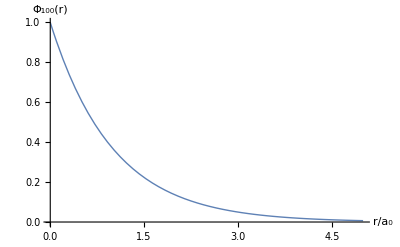

```mathematica
p = Plot[Exp[-x], {x,0,5}, AxesLabel->{"r/a_0" // fs, "Φ_100(r)" // fs}, Ticks -> None, PlotStyle->Thick]

fs = Style[#, FontSize-> 16]&;
```

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/phy456-qmII" ]
```

/Users/pjoot/project/figures/phy456-qmII

```mathematica
peeters`exportForLatex["hydrogenGroundStateFig2", p]
```

{hydrogenGroundStateFig2.eps,hydrogenGroundStateFig2pn.png}